```mathematica
dx1=0;
dx2=0;
dx3=0;

ds1=0;
ds2=0;
ds3=0;



X[1]=-1/2;
X[2]=1;
X[3]=-1/2;
X[4]=1/2;
X[5]=-1;
X[6]=1/2;

Y[1]=Sqrt[3]/2;
Y[2]=0;
Y[3]=-Sqrt[3]/2;
Y[4]=Sqrt[3]/2;
Y[5]=0;
Y[6]=-Sqrt[3]/2;



Z[1]=0;
Z[2]=0;
Z[3]=0;
Z[4]=0;
Z[5]=0;
Z[6]=0;

For[i=1,i≤6,i++,S[i]=Sqrt[X[i]^2+Y[i]^2+Z[i]^2]];
For[i=1,i≤6,i++,VN[i]={X[i],Y[i],Z[i]}/S[i]];
For[i=1,i≤6,i++,VN1[i]={-Y[i],X[i],0}/Sqrt[X[i]^2+Y[i]^2]];
For[i=1,i≤6,i++,VN2[i]=Cross[VN[i],VN1[i]]];
Clear[S1,S2,kx,ky,LZ]
NSS[1]=-2S[1] VN[1];
NSS[2]=-S[2]VN[2];
NSS[3]=-2S[3]VN[3];
NSS[4]=-2S[4]VN[4];
NSS[5]=-S[5]VN[5];
NSS[6]=-2S[6]VN[6];

NDS[1]=S1[6]VN1[6]Exp[-I kx]+S1[2]VN1[2]+S1[3]VN1[3]+S2[6]VN2[6]Exp[-I kx]+S2[2]VN2[2]+S2[3]VN2[3];
NDS[2]=S1[1]VN1[1]+S1[3]VN1[3]+S2[3]VN2[3];
NDS[3]=S1[1]VN1[1]+S1[2]VN1[2]+S1[4]VN1[4]+S2[2]VN2[2];
NDS[4]=S1[3]VN1[3]+S1[5]VN1[5]+S1[6]VN1[6]+S2[3]VN2[3]+S2[5]VN2[5]+S2[6]VN2[6];
NDS[5]=S1[4]VN1[4]+S1[6]VN1[6]+S2[6]VN2[6];
NDS[6]=S1[4]VN1[4]+S1[5]VN1[5]+S1[1]VN1[1]Exp[I kx]+S2[5]VN2[5];

DTS1[1]=-VN1[1].(LZ[1]S[1]Cross[VN2[1],VN[1]])/ii;
DTS1[4]=-VN1[4].(LZ[4]S[4]Cross[VN2[4],VN[4]])/ii;

DTS1[2]=VN1[2].(S[2]Cross[VN[2],NDS[2]]+S2[2]Cross[VN2[2],NSS[2]]+S1[2]Cross[VN1[2],NSS[2]]);
DTS1[3]=VN1[3].(S[3]Cross[VN[3],NDS[3]]+S2[3]Cross[VN2[3],NSS[3]]+S1[3]Cross[VN1[3],NSS[3]]);
DTS1[5]=VN1[5].(S[5]Cross[VN[5],NDS[5]]+S2[5]Cross[VN2[5],NSS[5]]+S1[5]Cross[VN1[5],NSS[5]]);
DTS1[6]=VN1[6].(S[6]Cross[VN[6],NDS[6]]+S2[6]Cross[VN2[6],NSS[6]]+S1[6]Cross[VN1[6],NSS[6]]);

DTLZ[1]=VN2[1].(S[1]Cross[VN[1],NDS[1]]+S1[1]Cross[VN1[1],NSS[1]]);
DTLZ[4]=VN2[4].(S[4]Cross[VN[4],NDS[4]]+S1[4]Cross[VN1[4],NSS[4]]);
DTS2[2]=VN2[2].(S[2]Cross[VN[2],NDS[2]]+S2[2]Cross[VN2[2],NSS[2]]+S1[2]Cross[VN1[2],NSS[2]]);
DTS2[3]=VN2[3].(S[3]Cross[VN[3],NDS[3]]+S2[3]Cross[VN2[3],NSS[3]]+S1[3]Cross[VN1[3],NSS[3]]);
DTS2[5]=VN2[5].(S[5]Cross[VN[5],NDS[5]]+S2[5]Cross[VN2[5],NSS[5]]+S1[5]Cross[VN1[5],NSS[5]]);
DTS2[6]=VN2[6].(S[6]Cross[VN[6],NDS[6]]+S2[6]Cross[VN2[6],NSS[6]]+S1[6]Cross[VN1[6],NSS[6]]);



DNMM1D=CoefficientArrays[Flatten[{Table[DTS1[i],{i,1,6}],DTLZ[1],DTS2[2],DTS2[3],DTLZ[4],DTS2[5],DTS2[6]}]==0,Flatten[{Table[S1[i],{i,1,6}],LZ[1],S2[2],S2[3],LZ[4],S2[5],S2[6]}]][[2]];
Clear[HH1D]
MatrixForm[DNMM1D]
```

```mathematica
HH1D[kx_,ii_]:=-I({{0, 0, 0, 0, 0, 0, -1/ii, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, -1, -1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, -1, -2, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, -1/ii, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -1, -1}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -1, -2}, {2, -1/2, -1/2, 0, 0, -ⅇ^(-ⅈ kx), 0, 0, 0, 0, 0, 0}, {-1/2, 1, -1/2, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {-1/2, -1/2, 2, -1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, -1, 2, -1/2, -1/2, 0, 0, 0, 0, 0, 0}, {0, 0, 0, -1/2, 1, -1/2, 0, 0, 0, 0, 0, 0}, {-ⅇ^(ⅈ kx), 0, 0, -1/2, -1/2, 2, 0, 0, 0, 0, 0, 0}})
```

```mathematica
Eigensystem[HH1D[0,1.0]]
```

{{-2.31197+6.66023×10^-18 ⅈ,2.31197+1.88528×10^-18 ⅈ,1.89239+7.24275×10^-18 ⅈ,-1.89239-6.71474×10^-17 ⅈ,1.41421+1.3965×10^-17 ⅈ,-1.41421-8.39888×10^-18 ⅈ,0.809192+1.91927×10^-17 ⅈ,-0.809192+4.76808×10^-17 ⅈ,0.647195+9.81124×10^-17 ⅈ,-0.647195-4.48299×10^-17 ⅈ,-1.37473×10^-8+5.68478×10^-10 ⅈ,1.37473×10^-8-5.68478×10^-10 ⅈ},{{3.70866×10^-19-0.180782 ⅈ,-6.00258×10^-18+0.180782 ⅈ,-4.78301×10^-18+0.342908 ⅈ,5.51036×10^-19-0.180782 ⅈ,1.54448×10^-18+0.180782 ⅈ,8.29685×10^-18+0.342908 ⅈ,0.417962+1.49181×10^-18 ⅈ,-0.0431315-5.57723×10^-18 ⅈ,-0.37483-3.38097×10^-18 ⅈ,0.417962+0. ⅈ,-0.0431315-3.35562×10^-18 ⅈ,-0.37483+6.6164×10^-18 ⅈ},{-5.84361×10^-19+0.180782 ⅈ,2.37934×10^-19-0.180782 ⅈ,-2.39861×10^-18-0.342908 ⅈ,3.04479×10^-18+0.180782 ⅈ,-1.98849×10^-19-0.180782 ⅈ,-4.53407×10^-18-0.342908 ⅈ,0.417962+0. ⅈ,-0.0431315-3.40053×10^-19 ⅈ,-0.37483+4.53077×10^-18 ⅈ,0.417962-6.98027×10^-18 ⅈ,-0.0431315-4.35253×10^-18 ⅈ,-0.37483+8.41926×10^-18 ⅈ},{-0.07561+4.50382×10^-17 ⅈ,-0.22683-1.68131×10^-17 ⅈ,-0.46593+3.71212×10^-17 ⅈ,0.07561-3.36882×10^-17 ⅈ,0.22683-2.68307×10^-17 ⅈ,0.46593+0. ⅈ,7.12918×10^-17+0.143084 ⅈ,-2.82111×10^-17-0.0232193 ⅈ,6.42961×10^-17+0.45247 ⅈ,-6.76092×10^-17-0.143084 ⅈ,-5.42731×10^-17+0.0232193 ⅈ,3.4464×10^-17-0.45247 ⅈ},{-0.07561+4.7015×10^-17 ⅈ,-0.22683-7.47736×10^-17 ⅈ,-0.46593-4.30428×10^-17 ⅈ,0.07561+1.04655×10^-17 ⅈ,0.22683-4.36166×10^-17 ⅈ,0.46593+0. ⅈ,-9.89972×10^-17-0.143084 ⅈ,1.03564×10^-16+0.0232193 ⅈ,1.34842×10^-17-0.45247 ⅈ,-2.65595×10^-17+0.143084 ⅈ,4.21296×10^-17-0.0232193 ⅈ,2.94778×10^-17+0.45247 ⅈ},{1.34808×10^-17-0.381 ⅈ,-2.16375×10^-17+0.127 ⅈ,1.59305×10^-17+0.127 ⅈ,5.28723×10^-18+0.381 ⅈ,-1.09155×10^-17-0.127 ⅈ,7.00139×10^-18-0.127 ⅈ,-0.538816-2.29736×10^-17 ⅈ,0.179605+2.64067×10^-17 ⅈ,1.501×10^-16-2.84943×10^-17 ⅈ,0.538816+0. ⅈ,-0.179605+3.12074×10^-17 ⅈ,-9.00102×10^-16-1.71899×10^-17 ⅈ},{-8.90967×10^-18+0.381 ⅈ,8.68653×10^-18-0.127 ⅈ,-3.64791×10^-17-0.127 ⅈ,-2.15583×10^-19-0.381 ⅈ,4.1825×10^-17+0.127 ⅈ,1.98303×10^-17+0.127 ⅈ,-0.538816-1.78302×10^-17 ⅈ,0.179605+6.1716×10^-17 ⅈ,-9.27183×10^-17-6.19249×10^-17 ⅈ,0.538816+0. ⅈ,-0.179605+2.4126×10^-17 ⅈ,3.19844×10^-16+2.94234×10^-17 ⅈ},{-3.52511×10^-17-0.187274 ⅈ,1.89025×10^-16+0.187274 ⅈ,-1.79507×10^-16-0.230373 ⅈ,-1.51903×10^-16-0.187274 ⅈ,-5.07325×10^-17+0.187274 ⅈ,-4.59727×10^-17-0.230373 ⅈ,-0.15154+4.23833×10^-17 ⅈ,0.489496-4.16071×10^-16 ⅈ,-0.337956+3.46467×10^-16 ⅈ,-0.15154+1.29153×10^-16 ⅈ,0.489496+0. ⅈ,-0.337956-5.09304×10^-17 ⅈ},{2.41276×10^-18+0.187274 ⅈ,7.08196×10^-17-0.187274 ⅈ,4.33883×10^-17+0.230373 ⅈ,-2.40346×10^-17+0.187274 ⅈ,-1.10427×10^-16-0.187274 ⅈ,-3.64692×10^-17+0.230373 ⅈ,-0.15154-8.07856×10^-18 ⅈ,0.489496-1.01109×10^-16 ⅈ,-0.337956+1.9996×10^-16 ⅈ,-0.15154+2.61558×10^-17 ⅈ,0.489496+0. ⅈ,-0.337956-1.55061×10^-16 ⅈ},{-5.7278×10^-16+0.127954 ⅈ,-5.33564×10^-16+0.383862 ⅈ,-4.84626×10^-16-0.0207641 ⅈ,-1.44799×10^-16-0.127954 ⅈ,9.36296×10^-16-0.383862 ⅈ,-3.36452×10^-16+0.0207641 ⅈ,0.0828112+3.93257×10^-16 ⅈ,0.510306+0. ⅈ,-0.261872+3.31512×10^-16 ⅈ,-0.0828112+1.24268×10^-16 ⅈ,-0.510306-1.51919×10^-15 ⅈ,0.261872+7.79707×10^-16 ⅈ},{1.92551×10^-16-0.127954 ⅈ,2.02411×10^-16-0.383862 ⅈ,2.20198×10^-16+0.0207641 ⅈ,2.21838×10^-16+0.127954 ⅈ,4.52105×10^-17+0.383862 ⅈ,1.41217×10^-16-0.0207641 ⅈ,0.0828112+1.14324×10^-16 ⅈ,0.510306+0. ⅈ,-0.261872+2.66274×10^-16 ⅈ,-0.0828112+1.91748×10^-16 ⅈ,-0.510306-1.22834×10^-16 ⅈ,0.261872-1.17794×10^-16 ⅈ},{0.408248-8.32667×10^-17 ⅈ,0.408248+4.16334×10^-17 ⅈ,0.408248-8.32667×10^-17 ⅈ,0.408248-1.11022×10^-16 ⅈ,0.408248+0. ⅈ,0.408248-2.77556×10^-17 ⅈ,2.3208×10^-10+5.61232×10^-9 ⅈ,2.3208×10^-10+5.61232×10^-9 ⅈ,-5.04796×10^-17-5.09195×10^-16 ⅈ,2.3208×10^-10+5.61232×10^-9 ⅈ,2.3208×10^-10+5.61232×10^-9 ⅈ,9.35174×10^-18-2.21863×10^-16 ⅈ},{0.408248-5.55112×10^-17 ⅈ,0.408248+2.08167×10^-17 ⅈ,0.408248-7.63278×10^-17 ⅈ,0.408248-1.04083×10^-16 ⅈ,0.408248+0. ⅈ,0.408248-2.77556×10^-17 ⅈ,-2.3208×10^-10-5.61232×10^-9 ⅈ,-2.3208×10^-10-5.61232×10^-9 ⅈ,-5.52643×10^-17-5.41691×10^-16 ⅈ,-2.3208×10^-10-5.61232×10^-9 ⅈ,-2.3208×10^-10-5.61232×10^-9 ⅈ,7.10456×10^-18-2.30856×10^-16 ⅈ}}}

```mathematica
EE1D[kx_]:=Sort[Re[Eigenvalues[HH1D[kx,1.0]]]]
```

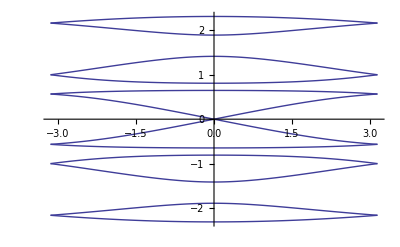

```mathematica
Plot[EE1D[kx],{kx,-Pi,Pi}]
```